```mathematica
Clear["Global`*"]
```

```mathematica
{{Tabs = ReadList["C:\\Users\\Alexandr\\Documents\\Source\\Repos\\Lab3\MassiveDots.txt", {Number,Number}];}, {□}}
Print[Tabs];
```

{{Null},{□}}

{{-1,0.675613},{-0.959184,0.678851},{-0.918367,0.682506},{-0.877551,0.686639},{-0.836735,0.691343},{-0.795918,0.69672},{-0.755102,0.702901},{-0.714286,0.710044},{-0.673469,0.718352},{-0.632653,0.728066},{-0.591837,0.739505},{-0.55102,0.753047},{-0.510204,0.769189},{-0.469388,0.78851},{-0.428571,0.811767},{-0.387755,0.839783},{-0.346939,0.873512},{-0.306122,0.913898},{-0.265306,0.961453},{-0.22449,1.0164},{-0.183673,1.077},{-0.142857,1.1393},{-0.102041,1.19802},{-0.0612245,1.24429},{-0.0204082,1.2691},{0.0204082,1.2691},{0.0612245,1.24429},{0.102041,1.19802},{0.142857,1.1393},{0.183673,1.077},{0.22449,1.0164},{0.265306,0.961453},{0.306122,0.913898},{0.346939,0.873512},{0.387755,0.839783},{0.428571,0.811767},{0.469388,0.78851},{0.510204,0.769189},{0.55102,0.753047},{0.591837,0.739505},{0.632653,0.728066},{0.673469,0.718352},{0.714286,0.710044},{0.755102,0.702901},{0.795918,0.69672},{0.836735,0.691343},{0.877551,0.686639},{0.918367,0.682505},{0.959184,0.678854},{1,0.675613}}

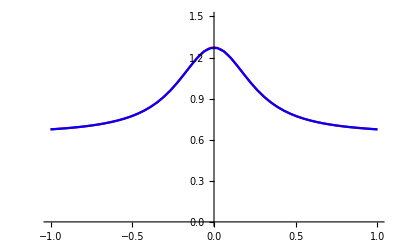

```mathematica
Show[Plot[1/ArcTan[1+10*x^2],{x,-1,1},PlotRange->{0,1.5}, PlotStyle->Red],ListLinePlot[Tabs,PlotStyle->Blue]]
```

```mathematica
Show[ListLinePlot[Tabs,PlotStyle->Blue],{x,-3,3},PlotRange->{.5,1.3}]
```

```mathematica
(* (4*x^3+2*x^2-4*x+2)^(Sqrt[2])+ArcSin[1/(5+x-x^2) -5] *)
```

```mathematica
(*1/ArcTan[1+10*x^2]*)
(*1/(1+10*x^2)*)
```

```mathematica
(*Show[Plot[1/ArcTan[1+10*x^2],{x,-3,3},PlotRange->{0,1.5}, PlotStyle->Red],ListLinePlot[Tabs,PlotStyle->Blue]]*)
```